```mathematica
Import["vicon_input.m"]
Import["datasets.m"]
```

```mathematica
SimpleAnnotator[currentDataset]
```

ListPointPlot3D::arrayerr: ViconTrackSection[currentDataset,8.,1.,1.] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[ViconTrackSection[currentDataset,8,1,1],PlotStyle→{RGBColor[0, 0, 1]}],ListPointPlot3D[ViconTrackSection[currentDataset,8,1,1],PlotStyle→{RGBColor[1, 0, 0]}]}].

ListPointPlot3D::arrayerr: ViconTrackSection[currentDataset,8.,1.,1.] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[ViconTrackSection[currentDataset,8,1,1],PlotStyle→{RGBColor[0, 0, 1]}],ListPointPlot3D[ViconTrackSection[currentDataset,8,1,1],PlotStyle→{RGBColor[1, 0, 0]}]}].

```mathematica
annotations = LoadAnnotations[];
whichTrack = 3;
tracks = ExtractReach[currentDataset, annotations,whichTrack];
```

```mathematica
planeData = ComputeTrackPlaneData[tracks, wristI];
(*m = PlotTracksArmAndPlane[currentDataset, 600, annotations[[1,2]], 2, tracks[[wristI,2]], tracks[[thumbI,2]], tracks[[pinkieI,2]], tracks[[elbowI,2]], tracks[[shoulderI,2]], planeData[[1,2]]];*)
```

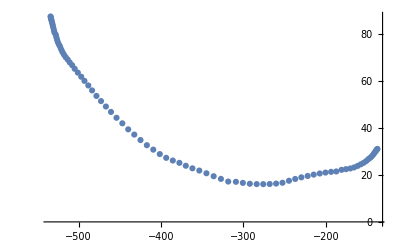

```mathematica
ListPlot[Transpose[planeData[[5,2]]]]
```

```mathematica
wristConic = ComputeConic2D[planeData[[5,2]]]
wristConicParametric = ComputeParametricEllipseFromConic2D[wristConic[[1,2]]]
```

{conicSolution→{0.0000102907,8.14227×10^-7,0.0000607411,0.0055419,-0.0161803,0.999854},conicMat→{{0.0000102907,4.07113×10^-7,0.00277095},{4.07113×10^-7,0.0000607411,-0.00809015},{0.00277095,-0.00809015,0.999854}}}

{conicCenter→{-274.61,135.031},axLens→{118.535,288.037},axVecs→{{0.00806878,0.999967},{-0.999967,0.00806878}},axAlpha→1.56273}

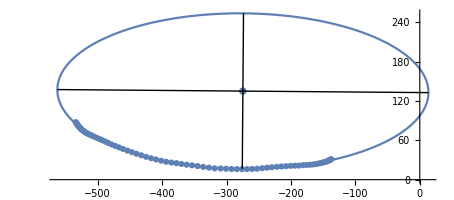

```mathematica
Show[{
ParametricPlot[HomToCart2D[
RigidTrans2D[wristConicParametric[[4,2]],wristConicParametric[[1,2,1]], wristConicParametric[[1,2,2]]].
CartToHom2D[Transpose[{{wristConicParametric[[2,2,1]] * Cos[ppTheta], wristConicParametric[[2,2,2]] * Sin[ppTheta]}}]]
], {ppTheta, -Pi, Pi}],
ListPlot[Transpose[planeData[[5,2]]]],
ListPlot[{wristConicParametric[[1,2]]}],
Graphics[
Line[{wristConicParametric[[1,2]] - wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]], wristConicParametric[[1,2]] + wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]]}
]],
Graphics[
Line[
{wristConicParametric[[1,2]] - wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]
, wristConicParametric[[1,2]] + wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]}
]]
(*,
ListPlot[Transpose[HomToCart2D[RigidTrans2D[,VTSWristCenter[[1]], VTSWristCenter[[2]]].CartToHom2D[{ParametricEllipsePt[WristAxLens[[1]], WristAxLens[[2]], uTheta]}]]]]*)
}]
```

```mathematica
PlotRangeParameter = 600;
Manipulate[Show[{
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[8]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[6]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[4]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[1]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[5]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],

Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[5]],ViconFrameMat[currentDataset, u][[1]],ViconFrameMat[currentDataset, u][[7]],ViconFrameMat[currentDataset, u][[5]]}]
],
Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[1]],ViconFrameMat[currentDataset, u][[8]],ViconFrameMat[currentDataset, u][[2]],ViconFrameMat[currentDataset, u][[3]],ViconFrameMat[currentDataset, u][[1]]}]
],
Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[8]],ViconFrameMat[currentDataset, u][[6]],ViconFrameMat[currentDataset, u][[4]],ViconFrameMat[currentDataset, u][[8]]}]
]
(*,
ParametricPlot3D[
ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]], ppTheta, Transpose[planeData[[2,2]]]]
,{ppTheta, -Pi, Pi}]*)
}]
, {u, annotations[[1,2,whichTrack,1]],annotations[[1,2,whichTrack,2]], 1}
]
```

Part::partw: Part 8 of ViconFrameMat[currentDataset,719] does not exist.

Part::partw: Part 8 of ViconFrameMat[currentDataset,719.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPointPlot3D::arrayerr: {ViconFrameMat[currentDataset,719.]⟦8⟧} must be a valid array or a list of valid arrays.

ListPointPlot3D::arrayerr: {ViconFrameMat[currentDataset,719.]⟦6⟧} must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPointPlot3D[{ViconFrameMat[currentDataset,719]⟦8⟧},PlotRange→{{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter}}],ListPointPlot3D[{ViconFrameMat[currentDataset,719]⟦6⟧},PlotRange→{{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter}}],ListPointPlot3D[{ViconFrameMat[currentDataset,719]⟦4⟧},PlotRange→{{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter}}],ListPointPlot3D[{currentDataset},PlotRange→{{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter},{-PlotRangeParameter,PlotRangeParameter}}],«1»,,,}].

```mathematica
Manipulate[Show[{
ListPointPlot3D[ViconTrackSection[currentDataset, 8, annotations[[1,2,whichTrack,1]], annotations[[1,2,whichTrack,2]]]],
ParametricPlot3D[
ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]], ppTheta, Transpose[planeData[[2,2]]]]
,{ppTheta, -Pi, Pi}],
ListPointPlot3D[Transpose[ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]],u, Transpose[planeData[[2,2]]]]],PlotStyle->{Green,PointSize[0.05]}],
ListPointPlot3D[ {ViconTrackSection[currentDataset, 8, annotations[[1,2,whichTrack,1]], annotations[[1,2,whichTrack,2]]][[1]]},PlotStyle->{Red,PointSize[0.05]}]
}]
, {u, -Pi,Pi}
]
```

Part::pkspec1: The expression whichTrack cannot be used as a part specification.

ListPointPlot3D::arrayerr: ViconTrackSection[currentDataset,8.,annotations⟦1,2,whichTrack,1⟧,annotations⟦1,2,whichTrack,2⟧] must be a valid array or a list of valid arrays.

Part::partd: Part specification planeData⟦4,2⟧ is longer than depth of object.

Part::partd: Part specification planeData⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification planeData⟦4,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPointPlot3D::arrayerr: Transpose[ParametricEllipse3DPt[wristConicParametric,planeData⟦4,2⟧,-3.14159,Transpose[planeData⟦2,2⟧]]] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

Part::pkspec1: The expression whichTrack cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Part::pkspec1: The expression whichTrack cannot be used as a part specification.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 3 in Take[{{{-352.761,-177.044,257.739,1.},{-352.707,-177.081,257.92,1.},{-352.633,-177.062,258.117,1.},{-352.478,-176.903,258.567,1.},{-352.759,-176.731,258.656,1.},{-352.656,-176.71,258.843,1.},{-352.746,-176.256,259.443,1.},{-352.838,-176.027,259.638,1.},{-352.081,-176.641,259.449,1.},{-351.99,-176.559,259.609,1.},{-352.398,-175.808,260.228,1.},{-352.237,-175.984,260.063,1.},«28»,{-349.712,-165.745,253.271,1.},{-349.262,-164.665,251.908,1.},{-348.776,-163.245,250.392,1.},{-348.155,-161.656,248.461,1.},{-347.354,-159.799,246.069,1.},{-347.111,-157.129,243.399,1.},{-345.805,-154.688,240.381,1.},{-344.212,-151.984,237.251,1.},{-342.887,-148.999,233.671,1.},{-341.091,-145.965,229.876,1.},«2629»},«6»,{«1»}},«2»,{1,3}].

Part::pkspec1: The expression whichTrack cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partd: Part specification wristConicParametric⟦4,2⟧ is longer than depth of object.

Part::partd: Part specification wristConicParametric⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification wristConicParametric⟦1,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 3 in Take[{{{-352.761,-177.044,257.739,1.},{-352.707,-177.081,257.92,1.},{-352.633,-177.062,258.117,1.},{-352.478,-176.903,258.567,1.},{-352.759,-176.731,258.656,1.},{-352.656,-176.71,258.843,1.},{-352.746,-176.256,259.443,1.},{-352.838,-176.027,259.638,1.},{-352.081,-176.641,259.449,1.},{-351.99,-176.559,259.609,1.},{-352.398,-175.808,260.228,1.},{-352.237,-175.984,260.063,1.},«28»,{-349.712,-165.745,253.271,1.},{-349.262,-164.665,251.908,1.},{-348.776,-163.245,250.392,1.},{-348.155,-161.656,248.461,1.},{-347.354,-159.799,246.069,1.},{-347.111,-157.129,243.399,1.},{-345.805,-154.688,240.381,1.},{-344.212,-151.984,237.251,1.},{-342.887,-148.999,233.671,1.},{-341.091,-145.965,229.876,1.},«2629»},«6»,{«1»}},«2»,{1,3}].

```mathematica
cnt = ComputeNearestThetas[wristConicParametric, tracks[[1,2]], Transpose[planeData[[2,2]]], planeData[[4,2]]];
cnt
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

{{distance→1.21075,theta→-2.64063,onEllipse→{-134.087,-282.81,173.07},interestPt→{-134.319,-283.696,172.278}},{distance→1.13395,theta→-2.64328,onEllipse→{-134.759,-282.734,173.181},interestPt→{-134.968,-283.642,172.535}},{distance→1.01381,theta→-2.6466,onEllipse→{-135.604,-282.638,173.318},interestPt→{-135.783,-283.5,172.816}},{distance→0.713837,theta→-2.65051,onEllipse→{-136.601,-282.526,173.479},interestPt→{-136.714,-283.186,173.232}},{distance→0.562413,theta→-2.65553,onEllipse→{-137.885,-282.384,173.684},interestPt→{-137.943,-282.943,173.703}},{distance→0.472704,theta→-2.66114,onEllipse→{-139.321,-282.227,173.911},interestPt→{-139.301,-282.544,174.261}},{distance→0.765983,theta→-2.6684,onEllipse→{-141.188,-282.028,174.2},interestPt→{-141.1,-282.251,174.927}},{distance→1.10732,theta→-2.67632,onEllipse→{-143.232,-281.814,174.51},interestPt→{-143.092,-282.028,175.587}},{distance→1.31932,theta→-2.6855,onEllipse→{-145.612,-281.571,174.862},interestPt→{-145.453,-281.85,176.142}},{distance→1.53789,theta→-2.69563,onEllipse→{-148.25,-281.309,175.243},interestPt→{-148.04,-281.379,176.765}},{distance→1.72199,theta→-2.70755,onEllipse→{-151.368,-281.011,175.679},interestPt→{-151.139,-281.069,177.385}},{distance→1.7467,theta→-2.72073,onEllipse→{-154.838,-280.691,176.148},interestPt→{-154.614,-280.743,177.879}},{distance→1.73467,theta→-2.73524,onEllipse→{-158.68,-280.353,176.645},interestPt→{-158.462,-280.354,178.366}},{distance→1.65839,theta→-2.75138,onEllipse→{-162.982,-279.994,177.177},interestPt→{-162.782,-279.98,178.823}},{distance→1.32315,theta→-2.76828,onEllipse→{-167.514,-279.637,177.708},interestPt→{-167.365,-279.652,179.023}},{distance→1.01753,theta→-2.78736,onEllipse→{-172.668,-279.258,178.278},interestPt→{-172.587,-279.573,179.242}},{distance→0.638775,theta→-2.80712,onEllipse→{-178.043,-278.891,178.833},interestPt→{-178.026,-279.33,179.297}},{distance→0.409462,theta→-2.83051,onEllipse→{-184.449,-278.492,179.445},interestPt→{-184.448,-278.832,179.673}},{distance→0.619008,theta→-2.85312,onEllipse→{-190.69,-278.143,179.988},interestPt→{-190.747,-278.626,179.606}},{distance→1.03986,theta→-2.87768,onEllipse→{-197.51,-277.804,180.526},interestPt→{-197.601,-278.275,179.603}},{distance→1.41657,theta→-2.9024,onEllipse→{-204.423,-277.505,181.01},interestPt→{-204.527,-277.873,179.646}},{distance→1.67335,theta→-2.92848,onEllipse→{-211.756,-277.238,181.46},interestPt→{-211.858,-277.48,179.807}},{distance→1.81615,theta→-2.95451,onEllipse→{-219.118,-277.018,181.845},interestPt→{-219.205,-277.011,180.031}},{distance→1.94653,theta→-2.98141,onEllipse→{-226.759,-276.842,182.177},interestPt→{-226.828,-276.533,180.256}},{distance→1.99568,theta→-3.00787,onEllipse→{-234.306,-276.72,182.436},interestPt→{-234.352,-275.996,180.577}},{distance→1.94393,theta→-3.03437,onEllipse→{-241.891,-276.647,182.63},interestPt→{-241.918,-275.535,181.036}},{distance→1.83055,theta→-3.06193,onEllipse→{-249.799,-276.625,182.761},interestPt→{-249.813,-275.156,181.669}},{distance→1.85253,theta→-3.08872,onEllipse→{-257.5,-276.655,182.82},interestPt→{-257.515,-275.059,181.88}},{distance→1.91088,theta→-3.11578,onEllipse→{-265.29,-276.738,182.81},interestPt→{-265.309,-275.037,181.94}},{distance→1.8879,theta→3.14014,onEllipse→{-273.14,-276.874,182.73},interestPt→{-273.164,-275.156,181.949}},{distance→1.99197,theta→3.11243,onEllipse→{-281.117,-277.067,182.577},interestPt→{-281.15,-275.226,181.818}},{distance→1.93301,theta→3.08363,onEllipse→{-289.397,-277.326,182.341},interestPt→{-289.439,-275.505,181.693}},{distance→1.4244,theta→3.0542,onEllipse→{-297.843,-277.65,182.019},interestPt→{-297.885,-276.278,181.64}},{distance→1.59332,theta→3.02478,onEllipse→{-306.263,-278.036,181.615},interestPt→{-306.31,-276.53,181.098}},{distance→2.15446,theta→2.99218,onEllipse→{-315.554,-278.535,181.074},interestPt→{-315.652,-276.417,180.689}},{distance→1.763,theta→2.96097,onEllipse→{-324.403,-279.081,180.463},interestPt→{-324.468,-277.423,179.867}},{distance→1.54237,theta→2.92962,onEllipse→{-333.24,-279.698,179.759},interestPt→{-333.271,-278.372,178.971}},{distance→1.38525,theta→2.89818,onEllipse→{-342.041,-280.384,178.962},interestPt→{-342.03,-279.391,177.996}},{distance→1.16035,theta→2.86703,onEllipse→{-350.688,-281.129,178.084},interestPt→{-350.654,-280.417,177.169}},{distance→0.787076,theta→2.83684,onEllipse→{-358.995,-281.914,177.15},interestPt→{-358.974,-281.409,176.547}},{distance→0.46034,theta→2.80739,onEllipse→{-367.019,-282.738,176.161},interestPt→{-367.005,-282.445,175.806}},{distance→0.144971,theta→2.77871,onEllipse→{-374.753,-283.595,175.124},interestPt→{-374.731,-283.729,175.073}},{distance→0.40136,theta→2.749,onEllipse→{-382.674,-284.539,173.974},interestPt→{-382.721,-284.634,174.361}},{distance→0.966307,theta→2.71894,onEllipse→{-390.587,-285.551,172.733},interestPt→{-390.702,-285.818,173.655}},{distance→1.32629,theta→2.689,onEllipse→{-398.36,-286.615,171.422},interestPt→{-398.474,-287.246,172.583}},{distance→1.639,theta→2.65807,onEllipse→{-406.269,-287.772,169.989},interestPt→{-406.346,-288.821,171.246}},{distance→2.00593,theta→2.62722,onEllipse→{-414.028,-288.984,168.481},interestPt→{-414.086,-290.397,169.904}},{distance→2.17762,theta→2.59578,onEllipse→{-421.794,-290.277,166.866},interestPt→{-421.791,-291.986,168.216}},{distance→2.44884,theta→2.56453,onEllipse→{-429.364,-291.619,165.184},interestPt→{-429.273,-293.712,166.452}},{distance→2.52661,theta→2.53338,onEllipse→{-436.754,-293.012,163.432},interestPt→{-436.621,-295.224,164.645}},{distance→2.73718,theta→2.50234,onEllipse→{-443.959,-294.453,161.613},interestPt→{-443.701,-296.983,162.625}},{distance→2.69987,theta→2.47113,onEllipse→{-451.033,-295.954,159.713},interestPt→{-450.741,-298.471,160.645}},{distance→2.82893,theta→2.44069,onEllipse→{-457.764,-297.467,157.793},interestPt→{-457.399,-300.137,158.654}},{distance→2.7558,theta→2.41211,onEllipse→{-463.923,-298.93,155.932},interestPt→{-463.527,-301.544,156.71}},{distance→2.63768,theta→2.38392,onEllipse→{-469.845,-300.413,154.041},interestPt→{-469.43,-302.922,154.742}},{distance→2.51744,theta→2.35695,onEllipse→{-475.361,-301.867,152.183},interestPt→{-474.956,-304.253,152.878}},{distance→2.26408,theta→2.33031,onEllipse→{-480.663,-303.337,150.302},interestPt→{-480.219,-305.506,150.776}},{distance→2.06236,theta→2.30679,onEllipse→{-485.219,-304.661,148.605},interestPt→{-484.745,-306.645,148.907}},{distance→1.51543,theta→2.28262,onEllipse→{-489.778,-306.046,146.826},interestPt→{-489.399,-307.502,147.01}},{distance→1.05408,theta→2.26183,onEllipse→{-493.597,-307.258,145.269},interestPt→{-493.284,-308.264,145.299}},{distance→0.446722,theta→2.23985,onEllipse→{-497.529,-308.558,143.595},interestPt→{-497.376,-308.977,143.57}},{distance→0.283678,theta→2.21919,onEllipse→{-501.124,-309.797,141.997},interestPt→{-501.162,-309.541,141.882}},{distance→0.405175,theta→2.20178,onEllipse→{-504.079,-310.855,140.633},interestPt→{-504.204,-310.471,140.601}},{distance→0.939952,theta→2.18519,onEllipse→{-506.827,-311.873,139.318},interestPt→{-507.207,-311.022,139.44}},{distance→1.23321,theta→2.17081,onEllipse→{-509.156,-312.763,138.167},interestPt→{-509.668,-311.653,138.328}},{distance→1.64112,theta→2.157,onEllipse→{-511.347,-313.626,137.051},interestPt→{-512.109,-312.226,137.444}},{distance→1.97065,theta→2.14422,onEllipse→{-513.333,-314.429,136.012},interestPt→{-514.234,-312.717,136.386}},{distance→2.03602,theta→2.13319,onEllipse→{-515.015,-315.127,135.107},interestPt→{-515.959,-313.362,135.48}},{distance→2.00019,theta→2.12307,onEllipse→{-516.532,-315.771,134.273},interestPt→{-517.449,-314.018,134.568}},{distance→1.72967,theta→2.11337,onEllipse→{-517.963,-316.392,133.468},interestPt→{-518.76,-314.874,133.7}},{distance→1.78771,theta→2.10394,onEllipse→{-519.331,-316.997,132.682},interestPt→{-520.191,-315.458,132.977}},{distance→1.66595,theta→2.09513,onEllipse→{-520.59,-317.566,131.944},interestPt→{-521.416,-316.152,132.249}},{distance→1.2979,theta→2.08719,onEllipse→{-521.708,-318.081,131.276},interestPt→{-522.384,-317.014,131.574}},{distance→0.905772,theta→2.07993,onEllipse→{-522.716,-318.553,130.663},interestPt→{-523.196,-317.816,130.878}},{distance→0.339494,theta→2.0732,onEllipse→{-523.639,-318.992,130.092},interestPt→{-523.843,-318.773,130.251}},{distance→0.727223,theta→2.06234,onEllipse→{-525.102,-319.703,129.168},interestPt→{-525.455,-319.071,129.234}},{distance→0.384012,theta→2.05651,onEllipse→{-525.876,-320.087,128.669},interestPt→{-526.035,-319.738,128.646}},{distance→0.238271,theta→2.04928,onEllipse→{-526.824,-320.564,128.049},interestPt→{-526.74,-320.467,127.848}},{distance→0.554421,theta→2.04316,onEllipse→{-527.614,-320.968,127.523},interestPt→{-527.328,-320.91,127.052}},{distance→0.853744,theta→2.0371,onEllipse→{-528.389,-321.37,127.},interestPt→{-527.905,-321.381,126.297}},{distance→1.09327,theta→2.03176,onEllipse→{-529.063,-321.724,126.539},interestPt→{-528.439,-321.734,125.641}},{distance→1.30871,theta→2.02615,onEllipse→{-529.763,-322.097,126.053},interestPt→{-528.993,-322.155,124.996}},{distance→1.50203,theta→2.02175,onEllipse→{-530.307,-322.391,125.67},interestPt→{-529.467,-322.32,124.427}},{distance→1.94726,theta→2.01727,onEllipse→{-530.855,-322.69,125.28},interestPt→{-529.779,-322.545,123.664}},{distance→2.0624,theta→2.01397,onEllipse→{-531.256,-322.911,124.992},interestPt→{-530.145,-322.675,123.271}}}

```mathematica
ListPlot[DisceteD[thetas]]
ListPlot[ComputeNorms[DisceteD[ellipsePositions]]]
ListPlot[ComputeNorms[DisceteD[originalPositions]]]
ListPlot[ComputeNorms[DisceteD[DisceteD[ellipsePositions]]]]
ListPlot[ComputeNorms[DisceteD[DisceteD[originalPositions]]]]
```

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

```mathematica
LinesAlong[ellipsePositions]
LinesAlong[DisceteD[ellipsePositions]]
LinesAlong[DisceteD[originalPositions]]
```

Part::partw: Part 1 of {} does not exist.

-Graphics3D-

Part::partw: Part 1 of {} does not exist.

-Graphics3D-

Part::partw: Part 1 of {} does not exist.

-Graphics3D-